```mathematica
Вариант 3;
```

Задание 1

```mathematica
1.1;
a = -1; b = 1;
f[x_] = 3^x;
n = 4;
Do[{Subscript[x, i] = Cos[Pi*(2*i + 1)/(2*(n + 1))], Subscript[f, i] = f[Subscript[x, i]]}, {i, 0, n}]
```

```mathematica
P[x_] = Sum[Product[(x - Subscript[x, i])/(Subscript[x, k] - Subscript[x, i]), {i, 0, k - 1}]*Product[(x - Subscript[x, i])/(Subscript[x, k] - Subscript[x, i]), {i, k + 1, n}]*Subscript[f, k], {k, 0, n}] // Simplify // Expand
```

1-1/4 3^(1-1/2 √(1/2 (5-√5))) √(1/5 (10-2 √5)) x+1/4 3^(1+1/2 √(1/2 (5-√5))) √(1/5 (10-2 √5)) x-1/4 3^(-1/2 √(1/2 (5-√5))) √(10-2 √5) x+1/4 3^(1/2 √(1/2 (5-√5))) √(10-2 √5) x+1/2 3^(1-1/2 √(1/2 (5+√5))) √(1/10 (5+√5)) x-1/2 3^(1+1/2 √(1/2 (5+√5))) √(1/10 (5+√5)) x-1/2 3^(-1/2 √(1/2 (5+√5))) √(1/2 (5+√5)) x+1/2 3^(1/2 √(1/2 (5+√5))) √(1/2 (5+√5)) x-4 x^2+3^(-1/2 √(1/2 (5-√5))) x^2+3^(1/2 √(1/2 (5-√5))) x^2+3^(-1/2 √(1/2 (5+√5))) x^2+3^(1/2 √(1/2 (5+√5))) x^2+(3^(1-1/2 √(1/2 (5-√5))) x^2)/(√5)+(3^(1+1/2 √(1/2 (5-√5))) x^2)/(√5)-(3^(1-1/2 √(1/2 (5+√5))) x^2)/(√5)-(3^(1+1/2 √(1/2 (5+√5))) x^2)/(√5)+3^(-1/2 √(1/2 (5-√5))) √(1/5 (10-2 √5)) x^3-3^(1/2 √(1/2 (5-√5))) √(1/5 (10-2 √5)) x^3+1/5 3^(-1/2 √(1/2 (5-√5))) √(10-2 √5) x^3-1/5 3^(1/2 √(1/2 (5-√5))) √(10-2 √5) x^3-3^(-1/2 √(1/2 (5+√5))) √(2/5 (5+√5)) x^3+3^(1/2 √(1/2 (5+√5))) √(2/5 (5+√5)) x^3+1/5 3^(-1/2 √(1/2 (5+√5))) √(2 (5+√5)) x^3-1/5 3^(1/2 √(1/2 (5+√5))) √(2 (5+√5)) x^3+(16 x^4)/5-4/5 3^(-1/2 √(1/2 (5-√5))) x^4-4/5 3^(1/2 √(1/2 (5-√5))) x^4-4/5 3^(-1/2 √(1/2 (5+√5))) x^4-4/5 3^(1/2 √(1/2 (5+√5))) x^4-(4 3^(-1/2 √(1/2 (5-√5))) x^4)/(√5)-(4 3^(1/2 √(1/2 (5-√5))) x^4)/(√5)+(4 3^(-1/2 √(1/2 (5+√5))) x^4)/(√5)+(4 3^(1/2 √(1/2 (5+√5))) x^4)/(√5)

```mathematica
Tbl = Table[{Subscript[x, i], Subscript[f, i]}, {i, 0, n}];
Pl[x_] = InterpolatingPolynomial[Tbl, x] // Simplify // Expand
Simplify[P[x] - Pl[x]] == 0
```

3^(1/4 √(10-2 √5)-1/2 √(1/2 (5-√5)))-1/2 3^(-1/2 √(1/2 (5-√5))) √(1/10 (25-5 √5)) x+1/2 3^(1/2 √(1/2 (5-√5))) √(1/10 (25-5 √5)) x-1/2 3^(1-1/2 √(1/2 (5-√5))) √(1/10 (5-√5)) x+1/2 3^(1+1/2 √(1/2 (5-√5))) √(1/10 (5-√5)) x+1/2 3^(1-1/2 √(1/2 (5+√5))) √(1/10 (5+√5)) x-1/2 3^(1+1/2 √(1/2 (5+√5))) √(1/10 (5+√5)) x-1/2 3^(-1/2 √(1/2 (5+√5))) √(1/2 (5+√5)) x+1/2 3^(1/2 √(1/2 (5+√5))) √(1/2 (5+√5)) x+3^(-1/2 √(1/2 (5-√5))) x^2+3^(-1/2 √(1/2 (5+√5))) x^2-4 3^(1/4 √(10-2 √5)-1/2 √(1/2 (5-√5))) x^2+3^(1/2 √(10-2 √5)-1/2 √(1/2 (5-√5))) x^2+3^(1/4 √(10-2 √5)-1/2 √(1/2 (5-√5))+1/2 √(1/2 (5+√5))) x^2+(3^(1-1/2 √(1/2 (5-√5))) x^2)/(√5)+(3^(1+1/2 √(10-2 √5)-1/2 √(1/2 (5-√5))) x^2)/(√5)-(3^(1+1/4 √(10-2 √5)-1/2 √(1/2 (5-√5))-1/2 √(1/2 (5+√5))) x^2)/(√5)-(3^(1+1/4 √(10-2 √5)-1/2 √(1/2 (5-√5))+1/2 √(1/2 (5+√5))) x^2)/(√5)+1/5 3^(-1/2 √(1/2 (5-√5))) √(2/5 (25-5 √5)) x^3-1/5 3^(1/2 √(1/2 (5-√5))) √(2/5 (25-5 √5)) x^3+3^(-1/2 √(1/2 (5-√5))) √(2/5 (5-√5)) x^3-3^(1/2 √(1/2 (5-√5))) √(2/5 (5-√5)) x^3-3^(-1/2 √(1/2 (5+√5))) √(2/5 (5+√5)) x^3+3^(1/2 √(1/2 (5+√5))) √(2/5 (5+√5)) x^3+1/5 3^(-1/2 √(1/2 (5+√5))) √(2 (5+√5)) x^3-1/5 3^(1/2 √(1/2 (5+√5))) √(2 (5+√5)) x^3-4/5 3^(-1/2 √(1/2 (5-√5))) x^4-4/5 3^(-1/2 √(1/2 (5+√5))) x^4+16/5 3^(1/4 √(10-2 √5)-1/2 √(1/2 (5-√5))) x^4-4/5 3^(1/2 √(10-2 √5)-1/2 √(1/2 (5-√5))) x^4-4/5 3^(1/4 √(10-2 √5)-1/2 √(1/2 (5-√5))+1/2 √(1/2 (5+√5))) x^4-(4 3^(-1/2 √(1/2 (5-√5))) x^4)/(√5)+(4 3^(-1/2 √(1/2 (5+√5))) x^4)/(√5)-(4 3^(1/2 √(10-2 √5)-1/2 √(1/2 (5-√5))) x^4)/(√5)+(4 3^(1/4 √(10-2 √5)-1/2 √(1/2 (5-√5))+1/2 √(1/2 (5+√5))) x^4)/(√5)

True

```mathematica
1.2;
M1 = Maximize[{D[f[x], {x, n + 1}], a <= x <= b}, x][[1]];
M2 = Minimize[{D[f[x], {x, n + 1}], a <= x <= b}, x][[1]];
M = Max[Abs[M1], Abs[M2]];
R = M/(((n + 1)!)*2^n) // N
Print["Ответ: оценка погрешности R <= ", R]
```

Ответ: оценка погрешности R <= 0.00250059

0.00250059

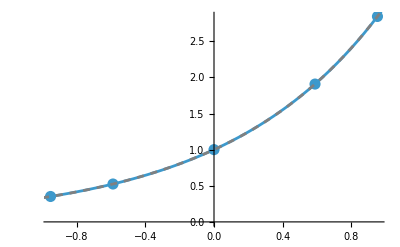

```mathematica
1.3;
Gr1 = ListPlot[Tbl, PlotStyle -> {PointSize[0.02]}];
Gr2 = Plot[f[x], {x, a, b}];
Gr3 = Plot[P[x], {x, a, b}, PlotStyle -> {Gray, Dashed}];
Show[Gr1, Gr2, Gr3]
```

Задание 2

Требуемая степень многочлена n = 12

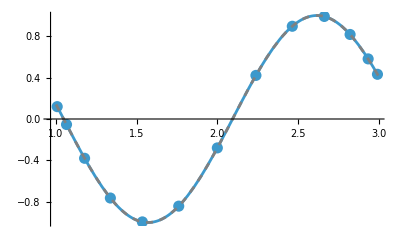

```mathematica
Clear[n, M, f, a, b, P, Pl];
f[x_] = Sin[3 x];
a = 1; b = 3; epsilon = 10^(-7);
M[n_] := Maximize[{Abs[D[f[x], {x, n + 1}]], a <= x <= b}, x][[1]];
n = 1;
While[N[(M[n]*(b - a)^(n + 1))/(((n + 1)!)*2^(2 n + 1))] > epsilon, n++];
Print["Требуемая степень многочлена n = ", n];
Do[{Subscript[x, i] = ((b - a)/2)*Cos[Pi*(2*i + 1)/(2*(n + 1))] + (a + b)/2, Subscript[f, i] = f[Subscript[x, i]]}, {i, 0, n}];
P[x_] = Sum[Product[(x - Subscript[x, i])/(Subscript[x, k] - Subscript[x, i]), {i, 0, k - 1}]*Product[(x - Subscript[x, i])/(Subscript[x, k] - Subscript[x, i]), {i, k + 1, n}]*Subscript[f, k], {k, 0, n}] // Expand // N;
Tbl = Table[{Subscript[x, i], Subscript[f, i]}, {i, 0, n}];
Gr1 = ListPlot[Tbl, PlotStyle -> {PointSize[0.02]}];
Gr2 = Plot[f[x], {x, a, b}];
Gr3 = Plot[P[x], {x, a, b}, PlotStyle -> {Gray, Dashed}];
Show[Gr1, Gr2, Gr3]
```

Задание 3

```mathematica
Clear[n, M, f, a, b, omega];
f[x_] = Sin[x];
a = 0; b = Pi/4; epsilon = 10^(-2);
Subscript[x, i_] := a + i*(b - a)/n;
n = 1;
While[
  (M = Maximize[{Abs[D[f[x], {x, n + 1}]], a <= x <= b}, x][[1]];
   omega[y_] = Product[y - Subscript[x, i], {i, 0, n}];
   Pomega = Maximize[{Abs[omega[y]], a <= y <= b}, y][[1]];
   N[M*Pomega/((n + 1)!)] > epsilon),
  n++];
Print["Требуемая степень n = ", n, "; минимальное число узлов = ", n + 1];
R = N[M*Pomega/((n + 1)!)];
Print["Ответ: число равноотстоящих узлов ", n + 1, ", оценка R <= ", R]
```

Требуемая степень n = 8; минимальное число узлов = 9

Ответ: число равноотстоящих узлов 9, оценка R <= 0.00542992

Задание 4

```mathematica
Clear[n, M, f, a, b];
f[x_] = Cos[x];
a = Pi/2; b = 3 Pi/4; n = 2;
M = Maximize[{Abs[D[f[x], {x, n + 1}]], a <= x <= b}, x][[1]];
R = M*(b - a)^(n + 1)/(((n + 1)!)*2^(2 n + 1)) // N;
Print["Ответ: оценка погрешности по оптимальным узлам R <= ", R]
```

Ответ: оценка погрешности по оптимальным узлам R <= 0.0025233